```mathematica
$Assumptions={};
```

```mathematica
TransformedDistribution[X/(Y + n), {X ~ UniformDistribution[{0, 1}], Y ~UniformDistribution[{0, 1}]}]
```

Syntax::sntxf: "{X~UniformDistribution[{0,1}]" cannot be followed by ",Y~UniformDistribution[{0,1}]}".

```mathematica
TransformedDistribution[u/(v+n),{u\[Distributed]UniformDistribution[{0,1}],v\[Distributed]UniformDistribution[{0,1}]}]
```

TransformedDistribution[x1/(x2+n),{x1\[Distributed]UniformDistribution[{0,1}],x2\[Distributed]UniformDistribution[{0,1}]}]

```mathematica
Mean[TransformedDistribution[x1/(x2+n),{x1\[Distributed]UniformDistribution[{0,1}],x2\[Distributed]UniformDistribution[{0,1}]}]]
```

1/2 (-Log[n]+Log[1+n])

```mathematica
FullSimplify[PDF[TransformedDistribution[x1/(x2+n),{x1\[Distributed]UniformDistribution[{0,1}],x2\[Distributed]UniformDistribution[{0,1}]}],x], Assumptions->{n >= 1, Element[n, Integers]}]
```

Piecewise[{{1/2+n, x≥0&&x+n x<1}, {1/2 (-n^2+1/x^2), n x<1&&x+n x≥1}, {0, True}}]

```mathematica
FullSimplify[1/4( (1/y - n)^2/2 + (1/y - n)n)]
```

1/8 (-n^2+1/y^2)

```mathematica
Integrate[%, {y, 0, 1/n}]
```

Integrate::idiv: Integral of -n^2/8+1/(8 y^2) does not converge on {0,1/n}.

∫_0^(1/n) 1/8 (-n^2+1/y^2)ⅆy

```mathematica
FullSimplify[Integrate[(u +n) , {u, 0, 1/y - n}]]
```

1/2 (-n^2+1/y^2)

```mathematica
FullSimplify[Integrate[(u +n) , {u, 0, 1}]]
```

1/2+n

```mathematica
TransformedDistribution[Log[u],u\[Distributed]UniformDistribution[{0,1}]]
```

TransformedDistribution[Log[x],x\[Distributed]UniformDistribution[{0,1}]]

```mathematica
PDF[TransformedDistribution[-Log[x],x\[Distributed]UniformDistribution[{0,1}]],x]
```

Piecewise[{{ⅇ^-x, x≥0}, {0, True}}]

```mathematica
Sum[Binomial[n, (n+k)/2] p^((n+k)/2) (1 - p)^(n - (n+k)/2) k, {k, -n, n}]
```

(1-p)^(n/2) ((1-p)^(n/2) DifferenceRoot[Function[{y,n},{-(2+n) (-n+n) p y[n]+(2+n) (-n+n) p y[1+n]-n (2+n+n) (-1+p) y[2+n]+n (2+n+n) (-1+p) y[3+n]==0,y[1]==0,y[2]==(1-p)^(1/2 (-1-n)) p^((1+n)/2) Binomial[n,(1+n)/2],y[3]==(1-p)^(1/2 (-1-n)) p^((1+n)/2) Binomial[n,(1+n)/2]+2 (1-p)^(1/2 (-2-n)) p^((2+n)/2) Binomial[n,(2+n)/2]}]][1+n]-p^(n/2) DifferenceRoot[Function[{y,n},{-(2+n) (-n+n) (-1+p) y[n]+(2+n) (-n+n) (-1+p) y[1+n]-n (2+n+n) p y[2+n]+n (2+n+n) p y[3+n]==0,y[1]==0,y[2]==(√(1-p) Binomial[n,1/2 (-1+n)])/(√p),y[3]==(2 (1-p) Binomial[n,1/2 (-2+n)])/p+(√(1-p) Binomial[n,1/2 (-1+n)])/(√p)}]][1+n])

```mathematica
FullSimplify[%]
```

(1-p)^n DifferenceRoot[Function[{y,n},{-(2+n) (-n+n) p y[n]+(2+n) (-n+n) p y[1+n]-n (2+n+n) (-1+p) y[2+n]+n (2+n+n) (-1+p) y[3+n]==0,y[1]==0,y[2]==(1-p)^(1/2 (-1-n)) p^((1+n)/2) Binomial[n,(1+n)/2],y[3]==(1-p)^(-n/2) p^(n/2) ((√p Binomial[n,(1+n)/2])/(√(1-p))-(2 p Binomial[n,(2+n)/2])/(-1+p))}]][1+n]-(-(-1+p) p)^(n/2) DifferenceRoot[Function[{y,n},{-(2+n) (-n+n) (-1+p) y[n]+(2+n) (-n+n) (-1+p) y[1+n]-n (2+n+n) p y[2+n]+n (2+n+n) p y[3+n]==0,y[1]==0,y[2]==(√(1-p) Binomial[n,1/2 (-1+n)])/(√p),y[3]==(-2 (-1+p) Binomial[n,1/2 (-2+n)]+√(-(-1+p) p) Binomial[n,1/2 (-1+n)])/p}]][1+n]

```mathematica
(p Exp[I u] + (1 - p) Exp[-I u])(p Exp[-I u] + (1 - p) Exp[I u])
```

(ⅇ^(ⅈ u) (1-p)+ⅇ^(-ⅈ u) p) (ⅇ^(-ⅈ u) (1-p)+ⅇ^(ⅈ u) p)

```mathematica
FullSimplify[(ⅇ^(ⅈ u) (1-p)+ⅇ^(-ⅈ u) p) (ⅇ^(-ⅈ u) (1-p)+ⅇ^(ⅈ u) p)]
```

Cos[u]^2+(1-2 p)^2 Sin[u]^2

```mathematica
FullSimplify[(p Exp[I u] + (1 - p) Exp[-I u])^n]
```

(Cos[u]+ⅈ (-1+2 p) Sin[u])^n

```mathematica
Limit[%, n -> Infinity]
```

lim_(n→∞) (Cos[u]+ⅈ (-1+2 p) Sin[u])^n

```mathematica
TrigToExp[Cos[u]+ⅈ (-1+2 p) Sin[u]]
```

ⅇ^(-ⅈ u)-ⅇ^(-ⅈ u) p+ⅇ^(ⅈ u) p

```mathematica
Sum[(Log[1 + n] - Log[n])/(2), {n, 0, Infinity}]
```

∑_(n=0)^∞ 1/2 (-Log[n]+Log[1+n])

```mathematica
Sum[Log[1 + n] - Log[n], {n, 1, Infinity}]
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ (-Log[n]+Log[1+n])

```mathematica
Sum[Log[1 + 1/n]/ϵ, {n, 1, Infinity}]
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ Log[1+1/n]/ϵ

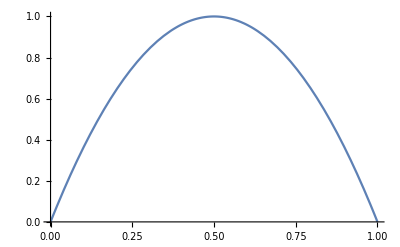

```mathematica
Plot[4x(1 - x), {x, 0, 1}]
```

```mathematica
Sum[Sqrt[n] 0.5^n, {n, 0, Infinity}]
```

1.34725

```mathematica
f[u_] := p Exp[I u] + (1 - p) Exp[-I u]
```

```mathematica
Integrate[1/(1 -  f[u]), {u, -Pi, Pi}]
```

Integrate::idiv: Integral of 1/(1+ⅇ^(-ⅈ u) (-1+p)-ⅇ^(ⅈ u) p) does not converge on {-π,π}.

∫_-π^π 1/(1-ⅇ^(-ⅈ u) (1-p)-ⅇ^(ⅈ u) p)ⅆu

```mathematica
Solve[z - p z^2 + 1 - p == 0, z]
```

{{z→(1-√(1+4 p-4 p^2))/(2 p)},{z→(1+√(1+4 p-4 p^2))/(2 p)}}

```mathematica
Residue[1/(z - p z^2 + 1 - p), z->1]
```

Residue[1/(1-p+z-p z^2),z→1]

```mathematica
Apart[1/((z - (1-√(1+4 p-4 p^2))/(2 p))(z - (1+√(1+4 p-4 p^2))/(2 p))), z]
```

p/(-1+p-z+p z^2)

```mathematica
TransformedDistribution[u/(v+n),{u\[Distributed]UniformDistribution[{0,1}],v\[Distributed]UniformDistribution[{0,1}]}]
```